```mathematica
ClearAll["Global`*"]
m=1;
l=20;
v=0.5;
g=9.8;
w=0.7;
period=2*Pi/w;
A=1;
tmax=1000;
w0 = Sqrt[g/l]
s=NDSolve[{m*l*theta''[t]+v theta'[t]+m g Sin[theta[t]]==A  Cos[w t],theta[0]==1,theta'[0]==0},theta,{t,0,tmax}];
```

0.7

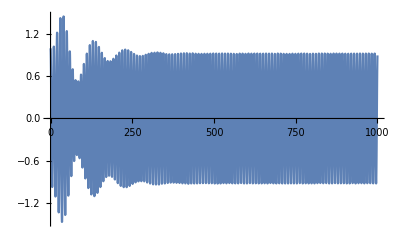

```mathematica
Plot[theta[x]/.s,{x,0,tmax}]
```

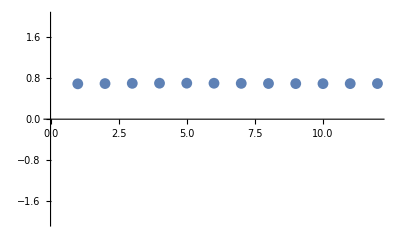

```mathematica
(*generate bifurcation plot*)
tdel=period;
result=Flatten[Table[theta[x]/.s,{x,400,500,tdel}]];
ListPlot[result,PlotRange->{All,{-2,2}}]
```